```mathematica
(* This function constructs the lowest order polynomial that matches the provided left [value, d1, ...] and right [value, d1, ...] and returns that polynomial as a univariate function. *)
PolyPiece[LeftValues_,RightValues_,interval_:{0,1}]:={
Clear[i,j,left,right,dds,newDiffs,row,newRow];
Clear[coefs,points,func];
(* Make "left" and "right" the same length by matching higher derivatives that are not provided for the other. *)
left={};
right={};
For[i=1,i≤Max[Length[LeftValues],Length[RightValues]],i++,{
If[i≤Length[LeftValues],AppendTo[left,LeftValues[[i]]],AppendTo[left,RightValues[[i]]]];
If[i≤Length[RightValues],AppendTo[right,RightValues[[i]]],AppendTo[right,LeftValues[[i]]]];
}];
(* Rescale the left and right derivaties by a factorial for correct usage in the divided difference table. *)
For[i=3,i≤Length[left],i++,{
left[[i]]/=Factorial[i-1];
right[[i]]/=Factorial[i-1];
}];
(* Make the coefficients a copy of the "left" set, they will be the first coefficients. We will compute the rest and add them to the end. *)
coefs=left[[1;;-1]];
(* Initialize the divided difference table to have the first difference between the first left and the first right. *)
If[Length[left]==1,dds={},dds= {(right[[1]]-left[[1]])/(interval[[2]]-interval[[1]])} ];
(* Compute all the interaction terms between the left and right, building up the divided difference table to level off at the last provided derivative. *)
For[i=2,i<Length[left],i++,{
(* Compute the interaction with the left. *)
newDiffs={dds[[1]]-left[[i]]};
(* Compute the interaction of all middle terms. *)
For[j=1,j<Length[dds],j++,{
AppendTo[newDiffs,dds[[j+1]]-dds[[j]]];
}];
(* Compute the interaction with the right. *)
AppendTo[newDiffs,right[[i]]-dds[[-1]]];
(* Add the newly computed row to the divided difference table. *)
dds=newDiffs/(interval[[2]]-interval[[1]]);
}];
(* Compute all of the coefficients for the Newton polynomial by completing the rest of the divided difference table. *)
row=Join[{left[[-1]]},dds,{right[[-1]]}];
While[Length[row]>1,{
newRow={};
For[i=1,i<Length[row],i++,{
AppendTo[newRow,(row[[i+1]]-row[[i]])/(interval[[2]]-interval[[1]])];
}];
AppendTo[coefs,newRow[[1]]];
row=newRow;
}];
(* Construct the coefficients and the points. *)
points=Join[ConstantArray[interval[[2]],Length[left]],ConstantArray[interval[[1]],Length[left]]];
coefs=Reverse[coefs];
(* Now we have all the coefficients necessary to construct a Newton interpolant. *)
func[x_]:={
total=coefs[[1]];
For[d=2,d≤Length[coefs],d++,total=coefs[[d]]+(x-points[[d]])total];
total
}[[1]];
Clear[i,j,left,right,dds,newDiffs,row,newRow];
(* Now we can return the polynomial function. *)
func
}[[1]];

(* Given a set of Newton polynomial coefficients and associated points, convert the polynomial to a Monomial basis (with all points equalling 0) by transforming the coefficients. *)
toMonomial[NewtonCoefs_,NewtonPoints_]:={
Clear[i,newCoefs,coefs,points];
coefs={NewtonCoefs[[1]]};
For[i=2,i≤Length[NewtonCoefs],i++,{
(* Compute the old coefficients multiplied by a constant (no shift to higher power). *)
newCoefs=Join[{0},-coefs*NewtonPoints[[i]]];
(* Add the last result to all existing values shifted to a higher power. *)
coefs=newCoefs+Join[coefs,{NewtonCoefs[[i]]}];
}];
(* Set the variable "points" to be all zeros. *)
points=ConstantArray[0,Length[coefs]];
Clear[i,newCoefs];
(* Return the simplified coefficients. *)
coefs
}[[1]];
```

```mathematica
l={x,x1,x2};
r={y,y1,y2};
int={u0,u1};
f=PolyPiece[l,r,int];
toMonomial[coefs,points];
(*coefs=Reverse[coefs];*)
fix[exp_]:=Collect[ExpandAll[exp]/.{(u1-u0)->w}/.{(u0*u1)->v,(u0^2 u1)->v u0,(u0 u1^2)->v u1,(u0^2 u1^2)->v^2,(u0^3 u1)->v u0^2,(u0^3 u1^2)-> v^2 u0},{x,x1,x2,y,y1,y2}];
coefs=fix[coefs];
(*Print["x^5  =  ",fix[coefs[[1]]]]
Print["x^4  =  ",fix[coefs[[2]]]]
Print["x^3  =  ",fix[coefs[[3]]]]
Print["x^2  =  ",fix[coefs[[4]]]]
Print["x^1  =  ",fix[coefs[[5]]]]
Print["x^0  =  ",fix[coefs[[6]]]]*)
f'[z];
Reduce[{
u0<u1,
ConditionalExpression[f'[z]>0,u0≤z≤u1],
x1≥0,
y1≥0,
{x,x1,x2,y,y1,y2}∈Reals
},{x,x1,x2,y,y1,y2}]
```

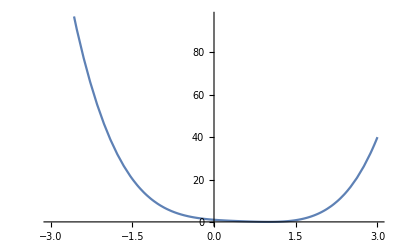

```mathematica
Plot[(x-1)(x+I)(x-I)(x-1),{x,-3,3}]
```

```mathematica
(* ----------------------------------------- *)
(* TESTING CODE FOR PRODUCING A DEMONSTRATION *)
int={0,1};
l={-2,2,3};
r={0,1,5};
Print["Left:  ",l]
Print["Right: ",r]
(* Construct polynomial piece. *)
f=PolyPiece[l,r,int];
Print["Coefs:\n ", coefs]
Print["Points:\n ", points]
funcStr=StringForm["``",coefs[[1]]];
For[i=2,i≤Length[coefs],i++,funcStr=StringForm["`` + (x - ``) (``)",coefs[[i]],points[[i]],funcStr]];
Print["Function:\n ",funcStr]
Print[]
Print["Function:\n ",Expand[f[x]]]
toMonomial[coefs,points];
Print["Coefs:\n ", coefs]
Print["Points:\n ", points]

(* Compute all of the derivatives to verify correctness. *)
Print[];
Print["f[x]:\n ",Expand[f[x]]]
leftEvals={f[int[[1]]]};
rightEvals={f[int[[2]]]};
For[i=2,i≤Max[Length[l],Length[r]],i++,{
df=Derivative[i-1][f];
Print[StringForm["f^(``)[x]:\n ``",i-1,Expand[df[x]]]];
AppendTo[leftEvals,df[int[[1]]]];
AppendTo[rightEvals,df[int[[2]]]];
}];
Print[];
Print["f[",int[[1]],"] = ",leftEvals,"  ",l]
Print["f[",int[[2]],"] = ",rightEvals,"  ",r]
Print[];

(* Compute a plot to see a visual of the function. *)
funcs={Expand[f[x]]};
labels={"f[x]"};
For[i=2,i≤Length[l],i++,{
AppendTo[funcs,Expand[Derivative[i-1][f][x]]];
AppendTo[labels,StringForm["f^(``)[x]",i-1]];
}];
Plot[funcs,{x,int[[1]],int[[2]]},PlotLabels->labels]
(* ------------------------------------------------- *)
```

Left:  {-2,2,3}

Right: {0,1,5}

Coefs:
 {4,1/2,-3/2,3/2,2,-2}

Points:
 {1,1,1,0,0,0}

Function:
 -2 + (x - 0) (…)

Function:
 -2+2 x+(3 x^2)/2+2 x^3-(15 x^4)/2+4 x^5

Coefs:
 {4,-15/2,2,3/2,2,-2}

Points:
 {0,0,0,0,0,0}

f[x]:
 -2+2 x+(3 x^2)/2+2 x^3-(15 x^4)/2+4 x^5

f^(RowBox[{)[x]:
 2+3 x+6 x^2-30 x^3+20 x^4

f^(RowBox[{)[x]:
 3+12 x-90 x^2+80 x^3

f[0] = {-2,2,3}  {-2,2,3}

f[1] = {0,1,5}  {0,1,5}

-Graphics-